Graphs
Original

```mathematica
ListPlot3D[Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\COVARIANCE\\cograph.dat", "Data"], InterpolationOrder->1]
```

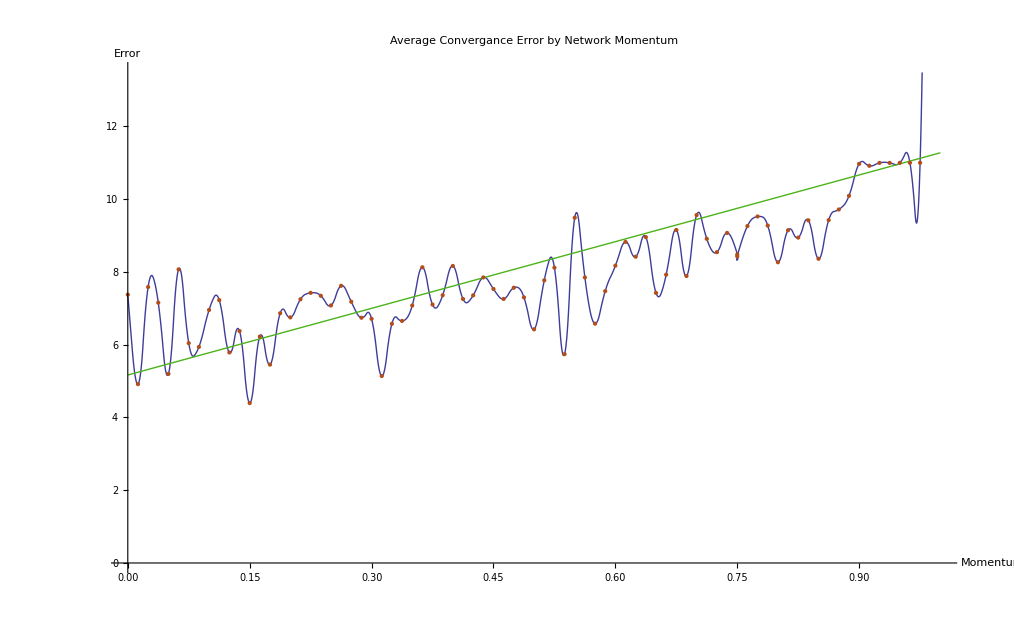

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\MM\\mmgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
Plot[Evaluate[Fit[data, {1,x}, x]],  {x,0,1},
 PlotStyle->{RGBColor[0.3,0.7,0.1]}],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["Momentum", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergance Error by Network Momentum", FontSize->36]]
```

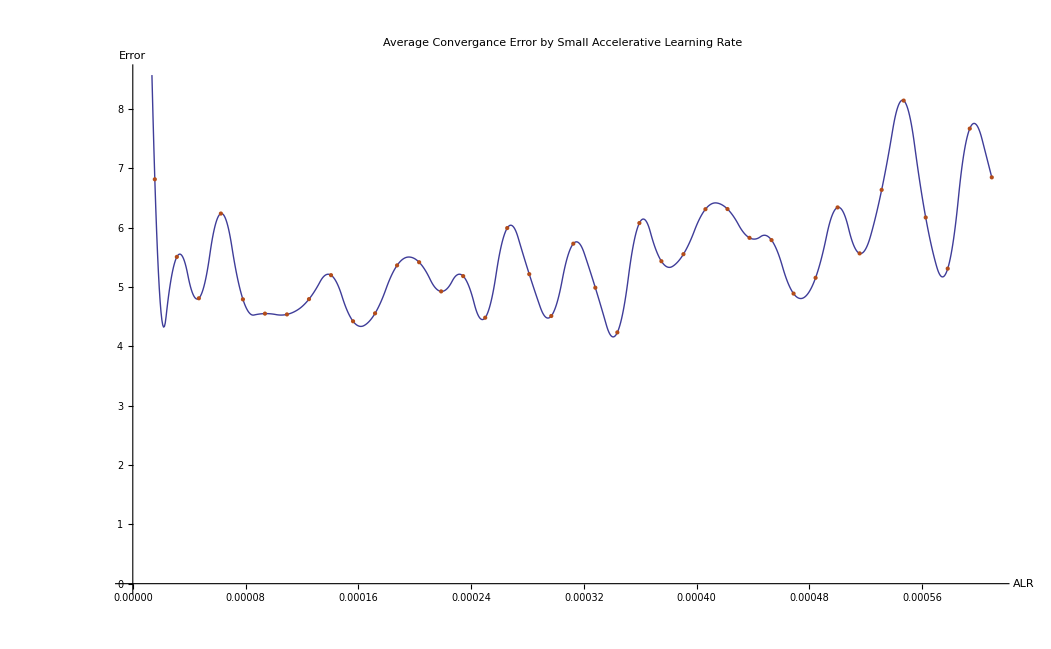

```mathematica
data2 = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Smallest\\smallgraph.dat", "Data"];
Show[ListLinePlot[data2, InterpolationOrder->2],
ListPlot[data2, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergance Error by Small Accelerative Learning Rate", FontSize->36]]
```

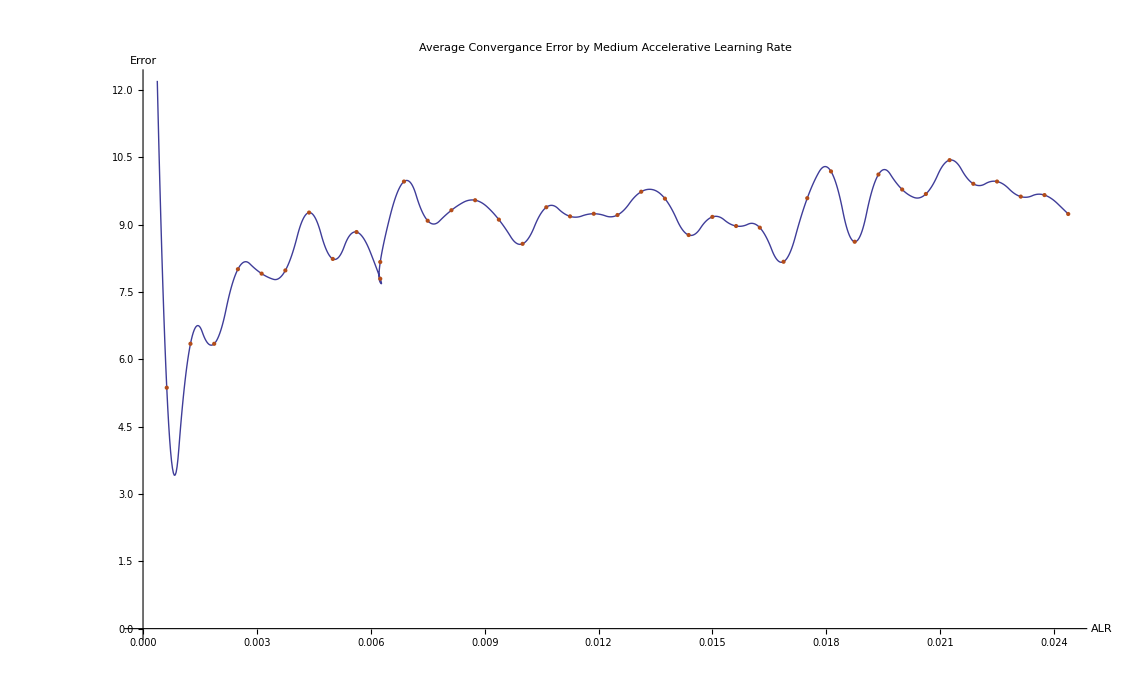

```mathematica
data3 = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Medium\\mediumgraph.dat", "Data"];
Show[ListLinePlot[data3, InterpolationOrder->2],
ListPlot[data3, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergance Error by Medium Accelerative Learning Rate", FontSize->36]]
```

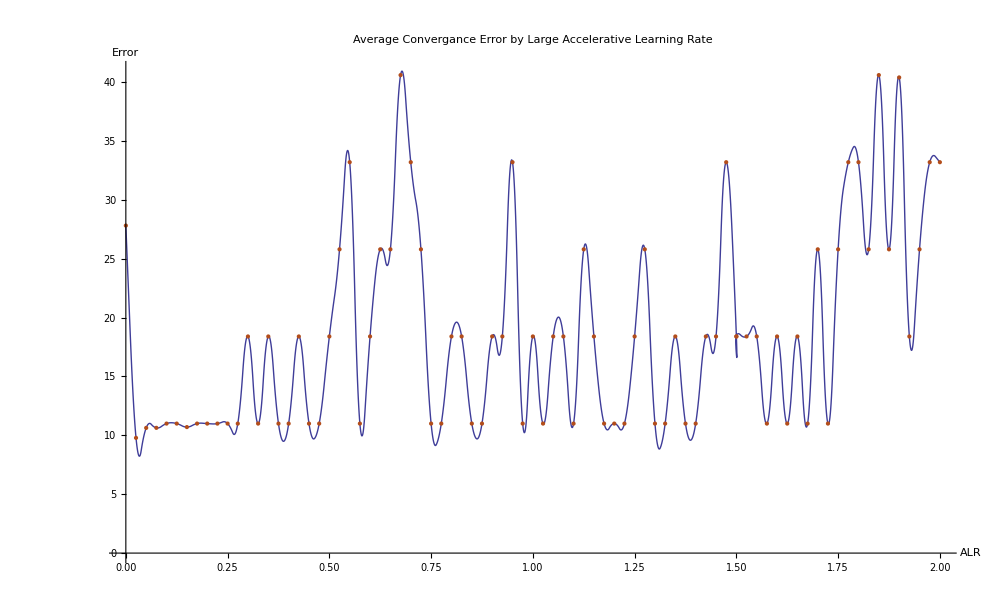

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Large\\broadgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergance Error by Large Accelerative Learning Rate", FontSize->36]]
```

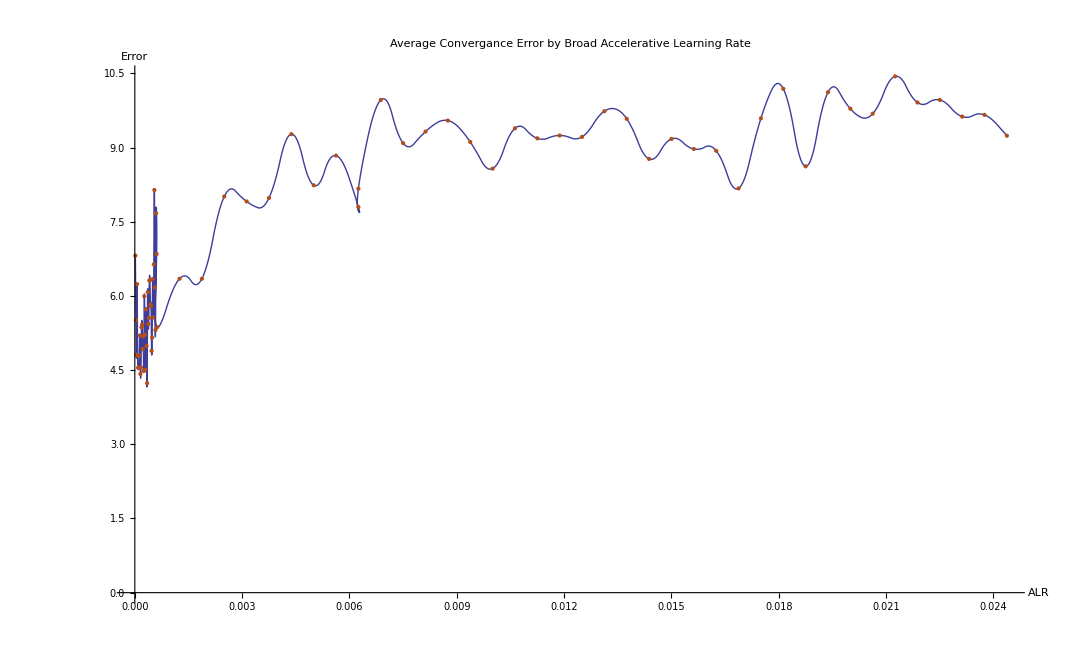

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\broad\\broadgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergance Error by Broad Accelerative Learning Rate", FontSize->36]]
```